# Vector mode in D=5

```mathematica
t- Integrate[1/f[z],z]
```

t-∫1/f[z]ⅆz

```mathematica
(*z=1/r*)
X={v,z,x1,x2,x3};
```

```mathematica
d=5;
```

```mathematica
G=1/z^2{{-f[z] z^2,-1,ϵ 1/2 htx[z] E^(-I ω v+I k x3),(*ϵ 1/2 hty[z] E^(-I ω v+I k x3)*)0,0},{-1, 0,0,0,0},
{ϵ 1/2 htx[z] E^(-I ω v+I k x3),0,1,0,ϵ 1/2 hzx[z] E^(-I ω v+I k x3)},{(*ϵ 1/2 hty[z] E^(-I ω v+I k x3)*)0,0,0,1,(*ϵ 1/2 hzy[z] E^(-I ω (t- Integrate[1/f[z],z])+I k x3)*)0},{0,0,ϵ 1/2 hzx[z] E^(-I ω v+I k x3),(*ϵ 1/2 hzy[z] E^(-I ω v+I k x3)*)0,1}}(*/.ϵ->0*)(*/.z->1/r*);
```

```mathematica
G//MatrixForm
```

(-f[z] | -1/z^2 | (ⅇ^(ⅈ k x3-ⅈ v ω) ϵ htx[z])/(2 z^2) | 0 | 0
-1/z^2 | 0 | 0 | 0 | 0
(ⅇ^(ⅈ k x3-ⅈ v ω) ϵ htx[z])/(2 z^2) | 0 | 1/z^2 | 0 | (ⅇ^(ⅈ k x3-ⅈ v ω) ϵ hzx[z])/(2 z^2)
0 | 0 | 0 | 1/z^2 | 0
0 | 0 | (ⅇ^(ⅈ k x3-ⅈ v ω) ϵ hzx[z])/(2 z^2) | 0 | 1/z^2)

```mathematica
IG=Inverse[G];
IG/.ϵ->0//MatrixForm
```

(0 | -z^2 | 0 | 0 | 0
-z^2 | z^4 f[z] | 0 | 0 | 0
0 | 0 | z^2 | 0 | 0
0 | 0 | 0 | z^2 | 0
0 | 0 | 0 | 0 | z^2)

```mathematica
IG.G//Simplify
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
Γ=Normal[Series[Table[1/2*Sum[IG[[i,l]]*(D[G[[j,l]],X[[k1]]]+D[G[[k1,l]],X[[j]]]-D[G[[j,k1]],X[[l]]]),{l,1,d}],{i,1,d},{j,1,d},{k1,1,d}],{ϵ,0,1}]];
```

```mathematica
Ric=Table[Sum[D[Γ[[k1,i,j]],X[[k1]]]-D[Γ[[k1,k1,i]],X[[j]]]+Sum[Γ[[q1,q1,k1]]Γ[[k1,i,j]]-Γ[[q1,i,k1]]Γ[[k1,q1,j]],{q1,1,d}],{k1,1,d}],{i,1,d},{j,1,d}](*Table[Sum[D[Γ[[i,j,k1]],X[[i]]]-D[Γ[[i,k1,i]],X[[j]]]+Sum[Γ[[i,i,p]]Γ[[p,j,k1]]-Γ[[i,j,p]]Γ[[p,i,k1]],{p,1,d}],{i,1,d}],{j,1,d},{k1,1,d}]*);
R=Normal[Series[Sum[IG[[i,j]]Ric[[i,j]],{i,1,d},{j,1,d}],{ϵ,0,1}]];
```

```mathematica
Ric//Dimensions
```

{5,5}

```mathematica
EinEq=Normal[Series[Ric+4 G,{ϵ,0,1}]]/.f->Function[z,1/z^2(1-z^4/zh^4)](*/.f->Function[z,1-z^4/zh^4]*)/.zh->1;
EinEq/.ϵ->0//Expand//Simplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

I output the three equations

```mathematica
EinEq[[1,3]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal(*//Collect[#,{htx'[z], hzx'[z]}]&*)
EinEq[[2,3]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal//Expand
EinEq[[3,5]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal(*//Collect[#,{htx'[z], hzx'[z]}]&*)
```

(ⅇ^(ⅈ (k x3-v ω)) ϵ (k^2 z htx[z]+k z ω hzx[z]+3 htx'[z]-3 z^4 htx'[z]-ⅈ z ω htx'[z]-z htx''[z]+z^5 htx''[z]))/(4 z)

(3 ⅇ^(ⅈ (k x3-v ω)) ϵ htx'[z])/(4 z)+1/4 ⅈ ⅇ^(ⅈ (k x3-v ω)) k ϵ hzx'[z]-1/4 ⅇ^(ⅈ (k x3-v ω)) ϵ htx''[z]

(ⅇ^(ⅈ (k x3-v ω)) ϵ (3 ⅈ k htx[z]+3 ⅈ ω hzx[z]-ⅈ k z htx'[z]+3 hzx'[z]+z^4 hzx'[z]-2 ⅈ z ω hzx'[z]-z hzx''[z]+z^5 hzx''[z]))/(4 z)

I eliminate the second derivative of htx

```mathematica
htppRule=Solve[(EinEq[[2,3]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal//Expand)==0,htx''[z]]//Flatten
```

{htx''[z]→(3 htx'[z]+ⅈ k z hzx'[z])/z}

I look for differential equation for hzx and htx

```mathematica
Solve[{0==EinEq[[1,3]]/.htppRule[[1]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal,
0==EinEq[[3,5]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal},{hzx''[z],htx'[z]}]//Simplify
```

{{hzx''[z]→((k^3 z-3 ⅈ k ω) htx[z]+(k^2 z-3 ⅈ ω) ω hzx[z]+ⅈ (k^2 z (-1+z^4)+ω (3 ⅈ+ⅈ z^4+2 z ω)) hzx'[z])/(z (-1+z^4) ω),htx'[z]→(k (-ⅈ k htx[z]-ⅈ ω hzx[z]+(-1+z^4) hzx'[z]))/ω}}

The sln below is obtained solving for each of the component of EinEq

```mathematica
sln=Solve[{0==EinEq[[1,3]]/.htppRule[[1]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal,
0==EinEq[[3,5]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal},{hzx''[z],htx'[z]}]//Simplify//Flatten;
```

```mathematica
eqns=sln[[All,1]]-sln[[All,2]]
```

{-((k^3 z-3 ⅈ k ω) htx[z]+(k^2 z-3 ⅈ ω) ω hzx[z]+ⅈ (k^2 z (-1+z^4)+ω (3 ⅈ+ⅈ z^4+2 z ω)) hzx'[z])/(z (-1+z^4) ω)+hzx''[z],htx'[z]-(k (-ⅈ k htx[z]-ⅈ ω hzx[z]+(-1+z^4) hzx'[z]))/ω}

```mathematica
(*eqns={(k z ω htx[z]+(-1+z^4) (3 ⅈ ω hzx[z]+(3+z^4-2 ⅈ z ω) hzx'[z]))/(z (-1+z^4)^2)+hzx''[z],(k z ω hty[z]+(-1+z^4) (3 ⅈ ω hzy[z]+(3+z^4-2 ⅈ z ω) hzy'[z]))/(z (-1+z^4)^2)+hzy''[z],-(ⅈ ω htx[z])/(-1+z^4)+ⅈ k hzx[z]+htx'[z]-(k (-1+z^4) hzx'[z])/ω,-(ⅈ ω hty[z])/(-1+z^4)+ⅈ k hzy[z]+hty'[z]-(k (-1+z^4) hzy'[z])/ω};*)
```

### massless KG, equation

Doubt:how to know whit which order we start the expansion? Why htx and hty start from 1 and the pure spatial entries start from 0?

```mathematica
NHexpansion={htx->Function[z, Sum[c[1,i](1-z)^i,{i,1,3}]](*,hty->Function[z, Sum[c[2,i](1-z)^i,{i,1,3}]]*),hzx->Function[z, Sum[c[2,i](1-z)^i,{i,0,3}]](*,hzy->Function[z, Sum[c[4,i](1-z)^i,{i,0,3}]]*)};
```

```mathematica
(*2 constants.*)
replNH={c[1,1]->ⅈ k c[2,0],c[2,1]->-(ⅈ (k^2-3 ⅈ ω) c[2,0])/(2 (2 ⅈ+ω)),c[1,2]->-((k (c1 (16+k^2 (-1+z)-5 ⅈ ω+3 ⅈ z (4 ⅈ+ω))+2 ⅈ (2 ⅈ+ω) c[2,0]))/(4 (-1+z) (2 ⅈ+ω))),c[2,2]->(c1 (k^2-3 ⅈ ω) (10+k^2 (-1+z)-8 ⅈ ω+6 ⅈ z (ⅈ+ω))+(2 ⅈ+ω) (-ⅈ k^2 (-5+3 z)+3 (7-5 z) ω) c[2,0])/(8 (-1+z) (2 ⅈ+ω) (4 ⅈ+ω)),c[1,3]->1/24 ((c1 k (-ⅈ k^4+6 k^2 (4 ⅈ+ω)+3 ⅈ (-64+28 ⅈ ω+ω^2)))/((2 ⅈ+ω) (4 ⅈ+ω))-(8 ⅈ k (c1-c[2,0]))/(-1+z)^2),c[2,3]->(ⅈ (c1 (k^6 (-1+z)^2+3 k^4 (-1+z)^2 (4+ⅈ ω)+k^2 (3 (-80+56 ⅈ ω+11 ω^2)+z^2 (-80+48 ⅈ ω+13 ω^2)-2 z (-128+84 ⅈ ω+19 ω^2))-3 ⅈ ω (-448+396 ⅈ ω+59 ω^2+z (608-576 ⅈ ω-82 ω^2)+z^2 (-224+228 ⅈ ω+31 ω^2)))-2 (k^2 (15-16 z+5 z^2)-3 ⅈ (29-40 z+15 z^2) ω) (-8+6 ⅈ ω+ω^2) c[2,0]))/(48 (-1+z)^2 (2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω))}/.{c[2,0]->c1};
```

```mathematica
NI=3;
```

```mathematica
Normal[Series[{(1-z)^2(*,(1-z)^2,(1-z)*),(1-z)}eqns/.NHexpansion//.replNH,{z,1,NI}]]/.c[2,0]->c1//Simplify
```

{0,0}

```mathematica
Solve[0==Series[{(1-z)^2(*,(1-z)^2,(1-z)*),(1-z)}eqns/.NHexpansion//.replNH,{z,1,3}]//Normal,Table[c[i,3],{i,1,2}]]//Simplify
```

{}

```mathematica
UVexpansion={htx->Function[z, Sum[b[1,i] z^i,{i,0,8}]],hzx->Function[z, Sum[b[2,i] z^i,{i,0,8}]]};
```

```mathematica
(*4 constants in the UV (2 vevs and 2 sources), 2 constants in the IR and of course ω ---> total 7 constants. If we set all the sources to zero we are left with a total of 5 constants, oout of which 1 can be set to 1 using the linearity of the equations... so, effectively, we have 4 constants. But the problem requires 6 integration constants! Explanation: both sources will be non-zero up to gauge.*)sub={ b[1,0]->-czx ω/k(*, b[2,0]->-czy ω/k*), b[2,0]->czx(*, b[4,0]->czy*), b[1,4]->vzx,b[2,4]->-(vzx ω)/k(*, b[4,4]->vzy*)};
repl={b[1,1]->0,b[2,1]->-ⅈ (k b[1,0]+ω b[2,0]),b[1,2]->-1/4 k (k b[1,0]+ω b[2,0]),b[2,2]->-1/4 ω (k b[1,0]+ω b[2,0]),b[1,3]->1/6 ⅈ k ω (k b[1,0]+ω b[2,0]),b[2,3]->1/12 ⅈ (k^2-ω^2) (k b[1,0]+ω b[2,0]),b[1,5]->-4/5 ⅈ vzx ω,b[2,5]->-(ⅈ vzx (k^2-5 ω^2))/(5 k),b[1,6]->1/12 vzx (k^2-5 ω^2),b[2,6]->-1/4 k vzx ω+(7 vzx ω^3)/(12 k)}/.sub
```

{b[1,1]→0,b[2,1]→0,b[1,2]→0,b[2,2]→0,b[1,3]→0,b[2,3]→0,b[1,5]→-4/5 ⅈ vzx ω,b[2,5]→-(ⅈ vzx (k^2-5 ω^2))/(5 k),b[1,6]→1/12 vzx (k^2-5 ω^2),b[2,6]→-1/4 k vzx ω+(7 vzx ω^3)/(12 k)}

```mathematica
NN=6;
```

```mathematica
Normal[Series[{z,1}eqns/.UVexpansion/.sub/.repl,{z,0,NN-1}]]//Simplify
```

{0,0}

```mathematica
Solve[0==Series[{z,1}eqns/.UVexpansion/.repl(*/.sub*),{z,0,3}]//Normal, Table[b[i,0],{i,1,2}]]//Simplify
```

{}

```mathematica
Solve[{0==(Series[{z,1}eqns/.UVexpansion/.repl(*/.sub*),{z,0,3}]//Normal)[[1]],0==(Series[{z,1}eqns/.UVexpansion/.repl(*/.sub*),{z,0,3}]//Normal)[[2]]},Table[b[i,0],{i,1,2}]]
```

{}

```mathematica
0==(Series[{z,1}eqns/.UVexpansion/.repl(*/.sub*),{z,0,3}]//Normal)[[2]]
```

0==(ⅈ k (k b[1,0]+ω b[2,0]))/ω+z^3 (4 b[1,4]+(4 k b[2,4])/ω)

```mathematica
0==(ⅈ k (k b[1,0]+ω b[2,0]))/ω+z^3 (4 b[1,4]+(4 k b[2,4])/ω)/.b[1,0]->-(ω b[2,0])/k
```

0==z^3 (4 b[1,4]+(4 k b[2,4])/ω)

```mathematica
0==4 b[1,4]+(4 k b[2,4])/ω//Solve[#,b[2,4]]&
```

{{b[2,4]→-(ω b[1,4])/k}}

```mathematica
{{b[1,0]->-(ω b[2,0])/k}}
```

{{b[1,0]→-(ω b[2,0])/k}}

#### Constrains on sources

```mathematica
nc=5;
```

```mathematica
exponential=Exp[-I ω  v(*(t- Integrate[1/f[z],z])*)] ⅇ^(ⅈ k x3);
```

```mathematica
ξup=exponential ϵ{0ζ1+0Sum[ζζ1[j] z^j,{j,1,nc}],1/z (ζ2 +Sum[ζζ2[j] z^j,{j,1,nc}]),ζ3+Sum[ζζ3[j] z^j,{j,1,nc}], ζ4+Sum[ζζ4[j] z^j,{j,1,nc}], ζ5+Sum[ζζ5[j] z^j,{j,1,nc}]};
ξ=G.ξup;
```

```mathematica
ξup
```

{0,(ⅇ^(ⅈ k x3-ⅈ v ω) ϵ (ζ2+z ζζ2[1]+z^2 ζζ2[2]+z^3 ζζ2[3]+z^4 ζζ2[4]+z^5 ζζ2[5]))/z,ⅇ^(ⅈ k x3-ⅈ v ω) ϵ (ζ3+z ζζ3[1]+z^2 ζζ3[2]+z^3 ζζ3[3]+z^4 ζζ3[4]+z^5 ζζ3[5]),ⅇ^(ⅈ k x3-ⅈ v ω) ϵ (ζ4+z ζζ4[1]+z^2 ζζ4[2]+z^3 ζζ4[3]+z^4 ζζ4[4]+z^5 ζζ4[5]),ⅇ^(ⅈ k x3-ⅈ v ω) ϵ (ζ5+z ζζ5[1]+z^2 ζζ5[2]+z^3 ζζ5[3]+z^4 ζζ5[4]+z^5 ζζ5[5])}

```mathematica
Dξ=Table[1/2(D[ξ[[i]],X[[j]]]+D[ξ[[j]],X[[i]]])-Sum[Γ[[kk,i,j]] ξ[[kk]],{kk,1,5}],{i,1,5},{j,1,5}];
```

```mathematica
Dξ2=Table[(D[ξup[[j]],X[[i]]])+Sum[Γ[[j,i,kk]] ξup[[kk]],{kk,1,5}],{i,1,5},{j,1,5}];
```

```mathematica
subg={};
```

```mathematica
GG=Coefficient[Normal[Series[Simplify[2 Dξ]+G,{ϵ,0,1}]]/.f->Function[z,1-z^4/zh^4]/.zh->1,ϵ];
```

```mathematica
(**)Normal[Series[Simplify[1/exponential GG]/.f->Function[z,1-z^4/zh^4]/.zh->1/.UVexpansion/.sub/.repl,{z,0,2}]]/.l->1 /.{ζ4->(ⅈ czy)/(2 k),ζ3->(ⅈ czx)/(2 k),ζζ3[1]->(czx ω)/(2 k),ζζ4[1]->(czy ω)/(2 k),ζ5->0, ζ2->0,ζζ2[1]->0,ζζ5[1]->0,ζζ2[2]->0,ζζ2[3]->0,ζζ2[4]->0,ζζ5[2]->0,ζζ5[3]->0,ζζ3[2]->-(ⅈ czx ω^2)/(4 k),ζζ4[2]->-(ⅈ czy ω^2)/(4 k),ζζ3[3]->-(czx ω^3)/(12 k),ζζ4[3]->-(czy ω^3)/(12 k),ζζ2[5]->0,ζζ5[4]->0,ζζ5[5]->0,ζζ3[4]->(ⅈ czx ω^4)/(48 k),ζζ4[4]->(ⅈ czy ω^4)/(48 k),ζζ3[5]->(czx ω (24+ω^4))/(240 k),ζζ4[5]->(czy ω (24+ω^4))/(240 k)}//FullSimplify//Factor//MatrixForm
```

(0 | 0 | (24 k vzx z^3-24 ⅈ czx ω^2-12 czx z ω^3+4 ⅈ czx z^2 ω^4+czx z^3 ω^5)/(48 k z) | (czy ω (24-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | 0
0 | 0 | (czx ω (24+24 z^4-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | (czy ω (24+24 z^4-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | 0
(24 k vzx z^3-24 ⅈ czx ω^2-12 czx z ω^3+4 ⅈ czx z^2 ω^4+czx z^3 ω^5)/(48 k z) | (czx ω (24+24 z^4-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | 0 | 0 | -(ω (-24 ⅈ czx k+24 vzx z^3-12 czx k z ω+4 ⅈ czx k z^2 ω^2+czx k z^3 ω^3))/(48 k z)
(czy ω (24-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | (czy ω (24+24 z^4-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | 0 | 0 | -(czy (24-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 z^2)
0 | 0 | -(ω (-24 ⅈ czx k+24 vzx z^3-12 czx k z ω+4 ⅈ czx k z^2 ω^2+czx k z^3 ω^3))/(48 k z) | -(czy (24-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 z^2) | 0)

```mathematica
vevTransformation={vzx->vzx-(czx ω^4)/24,vzy->vzy-(czy ω^4)/24};
```

```mathematica
(*both sources can be removed by a gauge transformation*)
Solve[{ζ4==(ⅈ czy)/(2 k),ζ3==(ⅈ czx)/(2 k)},{czy,czx}]
```

{{czy→-2 ⅈ k ζ4,czx→-2 ⅈ k ζ3}}

### Shooting Method

```mathematica
eqns
```

{-((k^3 z-3 ⅈ k ω) htx[z]+(k^2 z-3 ⅈ ω) ω hzx[z]+ⅈ (k^2 z (-1+z^4)+ω (3 ⅈ+ⅈ z^4+2 z ω)) hzx'[z])/(z (-1+z^4) ω)+hzx''[z],htx'[z]-(k (-ⅈ k htx[z]-ⅈ ω hzx[z]+(-1+z^4) hzx'[z]))/ω}

```mathematica
eqnlist[ω_,k_]:={-1/(z (-1+z^4) ω)((k^3 z-3 ⅈ k ω) htx[z]+(k^2 z-3 ⅈ ω) ω hzx[z]+ⅈ (k^2 z (-1+z^4)+ω (3 ⅈ+ⅈ z^4+2 z ω)) hzx'[z])+hzx''[z],htx'[z]-(k (-ⅈ k htx[z]-ⅈ ω hzx[z]+(-1+z^4) hzx'[z]))/ω};
```

```mathematica
(htx[z]/.NHexpansion/.c[2,0]->c1/.replNH)//Collect[#,{  (1-z)},Simplify]&
(hzx[z]/.NHexpansion/.c[2,0]->c1//.replNH)//Collect[#,{  (1-z)},Simplify]&
(htx[z]/.UVexpansion/.repl/. b[1,7]->0/. b[1,8]->0/.sub)//Collect[#,{  (z)},Simplify]&
(hzx[z]/.UVexpansion/.repl/. b[2,7]->0/. b[2,8]->0/.sub)//Collect[#,{  (z)},Simplify]&
```

ⅈ c1 k (1-z)-(c1 k (1-z)^2 (-12+k^2+3 ⅈ ω))/(4 (2 ⅈ+ω))+(c1 k (1-z)^3 (-ⅈ k^4+6 k^2 (4 ⅈ+ω)+3 ⅈ (-64+28 ⅈ ω+ω^2)))/(24 (2 ⅈ+ω) (4 ⅈ+ω))

c1-(c1 (1-z) (ⅈ k^2+3 ω))/(2 (2 ⅈ+ω))+(c1 (1-z)^2 (k^4+3 ω (-4 ⅈ+ω)))/(8 (2 ⅈ+ω) (4 ⅈ+ω))+(c1 (1-z)^3 (ⅈ k^6+3 k^2 (4+ⅈ ω) ω-3 k^4 (-4 ⅈ+ω)+3 ω (16+48 ⅈ ω+ω^2)))/(48 (2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω))

vzx z^4-(czx ω)/k-4/5 ⅈ vzx z^5 ω+1/12 vzx z^6 (k^2-5 ω^2)

czx-(vzx z^4 ω)/k-(ⅈ vzx z^5 (k^2-5 ω^2))/(5 k)+z^6 (-1/4 k vzx ω+(7 vzx ω^3)/(12 k))

```mathematica
NHhtx[c1_, ω_,k_][z_]:=ⅈ c1 k (1-z)-(c1 k (1-z)^2 (-12+k^2+3 ⅈ ω))/(4 (2 ⅈ+ω))+(c1 k (1-z)^3 (-ⅈ k^4+6 k^2 (4 ⅈ+ω)+3 ⅈ (-64+28 ⅈ ω+ω^2)))/(24 (2 ⅈ+ω) (4 ⅈ+ω));
NHhzx[c1_, ω_,k_][z_]:=c1-(c1 (1-z) (ⅈ k^2+3 ω))/(2 (2 ⅈ+ω))+(c1 (1-z)^2 (k^4+3 ω (-4 ⅈ+ω)))/(8 (2 ⅈ+ω) (4 ⅈ+ω))+(c1 (1-z)^3 (ⅈ k^6+3 k^2 (4+ⅈ ω) ω-3 k^4 (-4 ⅈ+ω)+3 ω (16+48 ⅈ ω+ω^2)))/(48 (2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω));
```

```mathematica
Ashtx[czx_,vzx_, ω_,k_][z_]:=vzx z^4-(czx ω)/k-4/5 ⅈ vzx z^5 ω+1/12 vzx z^6 (k^2-5 ω^2);
Ashzx[czx_,vzx_, ω_,k_][z_]:=czx-(vzx z^4 ω)/k-(ⅈ vzx z^5 (k^2-5 ω^2))/(5 k)+z^6 (-1/4 k vzx ω+(7 vzx ω^3)/(12 k));
```

```mathematica
F2[czx_?NumberQ,vzx_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:={htx[bound],hzx[bound],hzx'[bound]}/.NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[small]==Ashtx[czx,vzx,ω,k][small],hzx[small]==Ashzx[czx,vzx,ω,k][small],hzx'[small]==Ashzx[czx,vzx,ω,k]'[small]}],{htx,hzx},{z,small,bound},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
F2H[czx_?NumberQ,vzx_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:=NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[small]==Ashtx[czx,vzx,ω,k][small],hzx[small]==Ashzx[czx,vzx,ω,k][small],hzx'[small]==Ashzx[czx,vzx,ω,k]'[small]}],{htx,hzx},{z,small,bound},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
(*Integration from middle to z=1*)F1[c1_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:={htx[bound],hzx[bound],hzx'[bound]}/.NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[1-smallIR]==NHhtx[c1,ω,k][1-smallIR],hzx[1-smallIR]==NHhzx[c1,ω,k][1-smallIR],hzx'[1-smallIR]==NHhzx[c1,ω,k]'[1-smallIR]}],{htx,hzx},{z,bound, 1-smallIR},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
F1H[c1_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:=NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[1-smallIR]==NHhtx[c1,ω,k][1-smallIR],hzx[1-smallIR]==NHhzx[c1,ω,k][1-smallIR],hzx'[1-smallIR]==NHhzx[c1,ω,k]'[1-smallIR]}],{htx,hzx},{z,bound, 1-smallIR},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
(*Newton-Raphson method:at every step it changes the value of ϕvev and ω (starting from an initial guess that we give) until the integration from the left and the integration from the right give the same value for the field and its derivative in the middle: ϕ[bound], ϕ'[bound]*)
Clear[GG];
GG[k_,midd_]:=FindRoot[F2[czx,vzx,ω, k,midd]==F1[1,ω,k,midd],{czx,Tczx},{vzx,Tvzx},{ω,Tω},WorkingPrecision->wp,StepMonitor:>Print[Chop[F2[czx,vzx,ω,k,midd]-F1[1,ω,k,midd]]]];
```

```mathematica
smallIR=10^-10;
small=10^-6;
bound =5/10;
wp=55;
```

```mathematica
{Tczx,Tvzx,Tω}={1,1,-4-4I};
```

```mathematica
GG[1,bound]//Quiet
```

{0.920439273261883491548192272756686888358407621145097076-0.022919883616636391866821092169543732716237279452534855 ⅈ,-0.10325853713598723496551947884717159793057816699382657-0.054890614801217514025507800420666348687723875187184271 ⅈ,0.8025531916870509007640719689542122774199030648055076-0.5819723211221937873033891962212214358378072659884058 ⅈ}

{0.00763826050944007746693980995158551918331864494202081912+0.11457956049253710277875821413809836017224751170238946 ⅈ,-0.048120462996873558673453835558605332606070352088781379+0.018844193533810220172759951892671153062269312643778485 ⅈ,0.429259748611587504072048223143233296078722813107416-0.3649346485102824508488515164147468893675631368660561 ⅈ}

{-0.0203007986218868966621771877429657973134323618082498353+0.01028469854436188961560611551640451315171864184011 ⅈ,-0.02922817840344007620597659181605542329585375447616961+0.002820893456766850053941114126398818764787229356423867 ⅈ,0.236162907442756515355265526121629276262304715981735-0.1809570029707043269273286756746131313701467641649467 ⅈ}

{-0.0476681782659747369896261594531940208325608036408830855+0.002555547514893273051284508799172367997907887875072723 ⅈ,-0.00372161620955259235140969060058064239587138867461791-0.002988803825121438048131693887743256481279761408788261 ⅈ,0.206753137326688527324306435954825472944239588492922+0.1766384990489838374017832014058037163886635396096681 ⅈ}

{0.0141840812901847082140800376222446180996549869306940953+0.01462806579009674784064767507498889449379849921768122 ⅈ,0.00323907699360348975257196726605348256025806031919925-0.0076127486122172392421615318786203077725015961329139641 ⅈ,0.0649595899276598535824838844205201012522454302174429+0.04223534725096037640838628112201714186153550888653035 ⅈ}

{0.0039837908272656724720945802791212862997900313206330872+0.002555299062485503813041186192360066764685839602644363 ⅈ,0.004025757452449546119861766871841929505317326042226639-0.0036451528697549019373726825853406526640297909016300987 ⅈ,0.01463713389237123556687069061020190150732231834881+0.0373608198373990797057273873483375132060940729170145 ⅈ}

{0.0016674739569058438879916142303963364538467839591873699-0.002705605506954607488240955413067166920269173075384693 ⅈ,-0.004719375157992610786079020729595220320559326366861648-0.0004085399987215270833313097701434758957008291560318774 ⅈ,0.0225977017165364311549521024752876712514895196683-0.0300644123034325892229247435423704753489924511468791 ⅈ}

{0.0003280241396123248857129636402077325661406135759817633-0.00029991153560608379957379231341362230859093352351775 ⅈ,-0.00058093277908723529163129650607094845592514345276232-0.0005645411829808612872977525325038356533707221234178101 ⅈ,0.0055313614575371860782565235833122339969249253163203-0.0003830075599042233250961054911176710923189861936592 ⅈ}

{-2.5583876888533761188231619300535086511136662891464×10^-6+0.00001838368473338579198330544295471639523667606765862 ⅈ,0.00002908326177430390878703079547002232750297982657258-8.2752924821233276004601646783930285135947627538422×10^-6 ⅈ,-0.000102505349419583385845594147889884549601413271771+0.0002104364502023050368394126737328264865641887661418 ⅈ}

{2.59354968032501423760779708588814727837137794018×10^-8-1.015645493902885771382702128209067934522425817×10^-8 ⅈ,-3.21438586498166192637017776314701769056911115×10^-8-3.60390219080490796122794513994525107355913693832×10^-8 ⅈ,3.868157990582952785073985145180741373311642366×10^-7-4.212479735953472517524534492036788098213702×10^-10 ⅈ}

{0,0,0}

{0,0,0}

{0,0,0}

«1 more identical outputs»

{czx→0.03808788789675891437326773143928938531296726371190302329+0.04347016341806679561153479829951930970630876526807642717 ⅈ,vzx→-5.902073996509123357083819852341865907435752808777406995-2.699783399080445286820850364987648055094551812393513792 ⅈ,ω→-5.25112956436481597460344004897218620643926457200732537-4.739716346407794116001811259222483152487328575588132203 ⅈ}

```mathematica
result=%;
```

htx

```mathematica
sl1=F1H[c1,ω,k,bound]/.c1->1/.k->1/.result//Quiet;
sl2=F2H[czx,vzx, ω,k,bound]/.k->1/.result//Quiet;
```

```mathematica
sl2
```

{htx→InterpolatingFunction[…],hzx→InterpolatingFunction[…]}

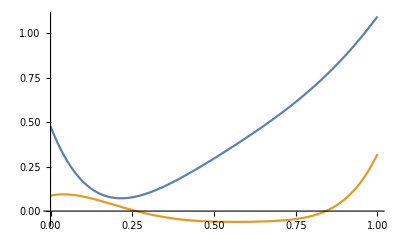

```mathematica
Subscript[z, h]=1;
(*sl=F1H[c1,c2, ω,k][bound]//.result/.k->1/.c1->1//Quiet
sl1=F2H[czx,czy,vzx,vzy, ω,k][bound]/.k->1/.result//Quiet*)
Show[Plot[{hzx[z]/.sl1//Re,hzx[z]/.sl1//Im},{z,0,bound},PlotRange->All],Plot[{hzx[z]/.sl2//Re,hzx[z]/.sl2//Im},{z,bound,zh},PlotRange->All],PlotRange->All]/.zh->Subscript[z, h]//Quiet
```

```mathematica
(*Extract the interpolation data points from f1 and f2*)
datahtx1=Table[{z,htx[z]/.sl2},{z,small,bound,(*choose an appropriate step size,e.g.,*)0.01}];
datahtx2=Table[{z,htx[z]/.sl1},{z,bound+0.01,1-smallIR,0.01}]; (*avoid redundancy at z=b*)

(*Combine the data from both interpolations*)
combinedDatahtx=Join[datahtx1,datahtx2];

(*Create a new interpolation function from the combined data*)
htxFunction2[z_]=Interpolation[combinedDatahtx];
```

InterpolatingFunction::dprec: The precision of input value {1.×10^-6} and/or the interpolation grid is insufficient to compute the value.

```mathematica
htxFunction[z_]:=Piecewise[{{htx[z]/.sl2,z<bound},{htx[z]/.sl1,z>=bound}}];
hzxFunction[z_]:=Piecewise[{{hzx[z]/.sl2,z<bound},{hzx[z]/.sl1,z>=bound}}];
```

```mathematica
hzxFunction[z]
```

Piecewise[{{InterpolatingFunction[…][z], z<1/2}, {InterpolatingFunction[…][z], z≥1/2}, {0, True}}]

```mathematica
htxFunction[small]
```

-0.0060318099547457147537098871920743427472881354360755794+0.4087932451567962556474322836746572248271208671925868 ⅈ

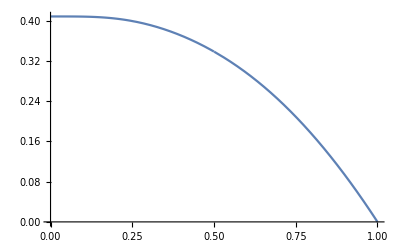

```mathematica
Plot[{htxFunction[z]//Im,htxFunction2[z]//Im},{z,0,1},PlotRange->All]
```

### Energy Computation

#### htx And hzx

(ⅇ^(ⅈ k x3-ⅈ v ω) ϵ htx[z])/(2 z^2)

```mathematica
(*htx[v_,z_,x3_]=1/(2 z^2)htxFunction[z] E^(-I ω v+I k x3)/.k->1/.result;
hzx[v_,z_,x3_]=1/(2 z^2)hzxFunction[z] E^(-I ω v+I k x3)/.k->1/.result;*)
```

```mathematica
ClearAll[hzx]
```

#### Master Scalar

```mathematica
gdd=G/.ϵ->0;
```

```mathematica
guu=IG/.ϵ->0;
```

```mathematica
ΓBG=Γ/.ϵ->0;
```

```mathematica
ClearAll[Φ]
```

```mathematica
CovCov=Sum[guu[[a,b]](D[D[Φ[v,z,x3], X[[a]]], X[[b]]]-Sum[Γ[[e,b,a]]D[Φ[v,z,x3], X[[e]]],{e,1,5}]),{a,1,5},{b,1,5}]//Simplify;
```

```mathematica
Pot=k^2 z^2+z^2 D[f[z], z]z+(-f[z] z^2);
```

```mathematica
MasterEq=CovCov-(*V*)Pot Φ[v,z,x3](*/.k->1*);
```

```mathematica
Pot/.f->Function[z,1/z^2(1-z^4/zh^4)]//Series[#,{z,0,4}]&
```

-3+k^2 z^2-z^4/zh^4+O[z]^5

```mathematica
MasterEq
```

-Φ[v,z,x3] (k^2 z^2-z^2 f[z]+z^3 f'[z])+z (z Φ^(0,0,2)[v,z,x3]+z^3 f'[z] Φ^(0,1,0)[v,z,x3]+z^2 f[z] (-Φ^(0,1,0)[v,z,x3]+z Φ^(0,2,0)[v,z,x3])+3 Φ^(1,0,0)[v,z,x3]-2 z Φ^(1,1,0)[v,z,x3])

```mathematica
Pot
```

k^2 z^2-z^2 f[z]+z^3 f'[z]

#### EF to FG

```mathematica
XFG={v+ Integrate[1/f[z],z],z,x1,x2,x3}
```

{v+∫1/f[z]ⅆz,z,x1,x2,x3}

```mathematica
X
```

{v,z,x1,x2,x3}

```mathematica
JacobianFG=Table[D[XFG[[i]],X[[j]]],{i,1,5},{j,1,5}]; (*This computes a 5x5 Jacobian matrix*)
```

```mathematica
JacobianFG
```

{{1,1/f[z],0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
GFG=Table[Sum[JacobianFG[[u,a]] G[[u,vv]] JacobianFG[[vv,b]],{u,1,5},{vv,1,5}],{a,1,5},{b,1,5}]//Simplify;
GFGh=SeriesCoefficient[GFG,{ϵ,0,1}]//Normal;
GFGh//MatrixForm
```

(0 | 0 | (ⅇ^(ⅈ (k x3-v ω)) htx[z])/(2 z^2) | 0 | 0
0 | 0 | (ⅇ^(ⅈ (k x3-v ω)) htx[z])/(2 z^2 f[z]) | 0 | 0
(ⅇ^(ⅈ (k x3-v ω)) htx[z])/(2 z^2) | (ⅇ^(ⅈ (k x3-v ω)) htx[z])/(2 z^2 f[z]) | 0 | 0 | (ⅇ^(ⅈ (k x3-v ω)) hzx[z])/(2 z^2)
0 | 0 | 0 | 0 | 0
0 | 0 | (ⅇ^(ⅈ (k x3-v ω)) hzx[z])/(2 z^2) | 0 | 0)

#### H Curly FG

Already translated

```mathematica
HFGtz=GFGh[[1,3]]-D[GFGh[[3,5]]/(I k), v]//Simplify;
HFGrz=GFGh[[2,3]]+(z^2 D[GFGh[[3,5]]/(I k), z]-1/f[z] D[GFGh[[3,5]]/(I k), v])+2z GFGh[[3,5]]/(I k)//Simplify;
```

#### H Curly EF

```mathematica
HEFtz=HFGtz;
HEFrz=HFGrz-1/f[z] HFGtz;
```

#### Boundary conditions

```mathematica
Normal[Series[MasterEq/.Φ->Function[{v,z,x3},E^(-I ω v) z^(Δ(*-1/2*))]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.k->1/.ω->0/.zh->1,{z,0,1}]]//Simplify
```

z^Δ (3-4 Δ+Δ^2)

```mathematica
Solve[%==0,Δ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Δ→1},{Δ→3}}

```mathematica
ΦExp=Function[z, Sum[p[i] z^i,{i,1,7}]];
```

```mathematica
hhtxExp=(ⅇ^(ⅈ k x3-ⅈ v ω) Ashtx[czx,vzx, ω,k][z])/(2 z^2)(*/.result*);
hhzxExp=(ⅇ^(ⅈ k x3-ⅈ v ω) Ashzx[czx,vzx, ω,k][z])/(2 z^2)(*/.result*);
```

To check

```mathematica
hEFrzEXP=HEFrz/.hzx->Function[z,Ashzx[czx,vzx, ω,k][z]]/.htx->Function[z,Ashtx[czx,vzx, ω,k][z]](*z^2∂_z hhzxExp(I k)^-1+2 z hhzxExp(I k)^-1-1/f[z](hhtxExp-∂_v hhzxExp(I k)^-1)*)/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1(*/.k->1*);
EXPEq=hEFrzEXP==(ⅇ^(ⅈ k x3-ⅈ v ω)D[ΦExp[z], z]-3/z ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]);
```

```mathematica
(*z^2∂_z hhzxExp+2 z hhzxExp-1/f[z](hhtxExp-∂_v hhzxExp)==(HEFrz/.hzx->Function[z,Ashzx[czx,vzx, ω,k][z]]/.htx->Function[z,Ashtx[czx,vzx, ω,k][z]])/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1//Simplify*)
```

```mathematica
EXPEq2=(HEFtz/.hzx->Function[z,Ashzx[czx,vzx, ω,k][z]]/.htx->Function[z,Ashtx[czx,vzx, ω,k][z]])(*hhtxExp-∂_v hhzxExp*)==3 f[z]/z ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]+f[z]/z^2(-z^2 D[(ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]), z])+1/z^2 D[(ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]), v]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1;
```

```mathematica
p1Rule=Solve[Series[{EXPEq},{z,0,0}]//Normal,p[1]]//Flatten(*//Simplify*)
```

{p[1]→0}

```mathematica
Solve[Series[EXPEq2,{z,0,-2}]//Normal,p[1]]//Flatten(*//Simplify*)
```

{p[1]→0}

```mathematica
p2Rule=Solve[Series[EXPEq,{z,0,1}]/.p1Rule//Normal,p[2]]//Flatten
```

{p[2]→0}

```mathematica
Solve[Series[EXPEq2,{z,0,-1}]/.p1Rule//Normal,p[2]]//Flatten
```

{p[2]→0}

```mathematica
Solve[Series[EXPEq,{z,0,2}]/.p1Rule/.p2Rule//Normal,p[3]]//Flatten
```

{}

```mathematica
p4Rule=Solve[Series[EXPEq,{z,0,3}](*/.p3Rule*)/.p1Rule/.p2Rule//Normal,p[4]]//Flatten
```

{p[4]→(2 ⅈ vzx ω)/k^2}

```mathematica
p5Rule=Solve[Series[EXPEq,{z,0,4}]/.p4Rule/.p1Rule/.p2Rule(*/.p3Rule*)//Normal,p[5]]//Flatten
```

{p[5]→-(vzx (k^2-5 ω^2))/(4 k^2)}

```mathematica
p6Rule=Solve[Series[EXPEq,{z,0,5}]/.p5Rule/.p1Rule/.p2Rule(*/.p3Rule*)/.p4Rule//Normal,p[6]]//Simplify//Flatten
```

{p[6]→(ⅈ vzx ω (3 k^2-7 ω^2))/(12 k^2)}

```mathematica
p7Rule=Solve[Series[EXPEq,{z,0,6}]/.p6Rule/.p1Rule/.p2Rule(*/.p3Rule*)/.p4Rule/.p5Rule//Normal,p[7]](*/.result/.k->1*)//Simplify//Flatten
```

{p[7]→0}

```mathematica
p3Rule=Solve[Series[EXPEq2,{z,0,1}]/.p1Rule/.p2Rule/.p4Rule//Normal,p[3]]//Flatten(*//Simplify*)
```

{p[3]→-(2 vzx)/k^2}

consistency check

```mathematica
Series[EXPEq2,{z,0,1}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule//Normal
```

True

```mathematica
Series[EXPEq2,{z,0,2}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule//Normal//Simplify
```

True

```mathematica
Series[EXPEq2,{z,0,2}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule//Normal//Simplify
```

True

```mathematica
Series[EXPEq2,{z,0,3}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule//Normal//Simplify
```

True

```mathematica
(*p7Rule=Solve[Series[EXPEq,{z,0,6}]/.p0Rule/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule//Normal,p[7]](*/.result/.k->1*)//Simplify//Flatten*)
```

```mathematica
(*p8Rule=Solve[Series[EXPEq,{z,0,7}]/.p0Rule/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule/.p7Rule//Normal,p[8]](*/.result/.k->1*)//Simplify//Flatten*)
```

```mathematica
(*p9Rule=Solve[Series[EXPEq,{z,0,8}]/.p0Rule/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule/.p7Rule/.p8Rule//Normal,p[9]](*/.result/.k->1*)//Simplify//Flatten*)
```

```mathematica
ClearAll[ΦExpBC]
```

```mathematica
ΦExpBC[zz_]:=ΦExp[z]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule/.p7Rule/.result/.k->1/.z->zz
```

```mathematica
ΦExpBC[small]
```

1.18040636910119672795379513441497380163666559825757935×10^-17+5.39960319047257539103602880946425130038597870796634723×10^-18 ⅈ

```mathematica
D[ΦExpBC[z], z]/.z->small
```

3.54121067711613901234774899346023348296660081008903797×10^-11+1.61988459633456054703970326251330618431632579785060553×10^-11 ⅈ

#### Differential Equation for Φ

```mathematica
hhzx[v_,z_,x3_]:=ⅇ^(ⅈ k x3-ⅈ v ω)/(2 z^2)hzxFunction[z];
hhtx[v_,z_,x3_]:=ⅇ^(ⅈ k x3-ⅈ v ω)/(2 z^2)htxFunction[z];
```

```mathematica
(*ClearAll[hhzx,hhtx]*)
```

```mathematica
(*z^2∂_z hhzxExp(I k)^-1+2 z hhzxExp(I k)^-1-1/f[z](hhtxExp-∂_v hhzxExp(I k)^-1)*)
```

```mathematica
HEFrz
```

-(ⅇ^(ⅈ (k x3-v ω)) (k htx[z]+ω hzx[z]))/(2 k z^2 f[z])+(ⅇ^(ⅈ (k x3-v ω)) (k htx[z]+ω hzx[z]-ⅈ z^2 f[z] hzx'[z]))/(2 k z^2 f[z])

```mathematica
ΦEqLHS=HEFrz/.htx->Function[z,htxFunction[z]]/.hzx->Function[z,hzxFunction[z]]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1(*/.k->1*);
ΦEqRHS=(ⅇ^(ⅈ k x3-ⅈ v ω)D[(z^3 Φ[z]), z]-3/z ⅇ^(ⅈ k x3-ⅈ v ω)(z^3 Φ[z]))/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1/.k->1(*/.x3->0*)/.v->0(*/.ω->0*)/.result(*//Simplify*);
```

```mathematica
ΦEq=(ΦEqLHS/.zh->1/.k->1/.x3->0/.v->0/.result)==(ΦEqRHS/.zh->1/.k->1/.x3->0/.v->0/.result);
```

```mathematica
ΦEqRHS
```

-3 ⅇ^(ⅈ x3) z^2 Φ[z]+ⅇ^(ⅈ x3) (3 z^2 Φ[z]+z^3 Φ'[z])

```mathematica
ΦFunction=Φ/.(NDSolve[{ΦEq,Φ[small]==ΦExpBC[small]/small^3(*,Φ'[small]==∂_z ΦExpBC[z]/.z->small*)},Φ,{z,small,1-smallIR},WorkingPrecision->30]//Flatten)
```

-6
InterpolatingFunction[{{1.00000000000000000000000000000 10  , 0.99999999990000000000000000000}}, <>]

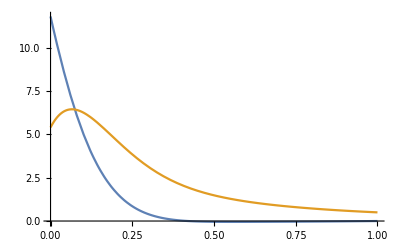

```mathematica
Plot[{(ΦFunction[z])//Re,(ΦFunction[z])//Im},{z,0,1},PlotRange->All]
```

#### Energy

```mathematica
ClearAll[Tdd]
```

```mathematica
Tdd=Table[1/2 D[(ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z]), X[[a]]](Conjugate[D[(z^3 ⅇ^(ⅈ k x3-ⅈ v ω)Φ[z]), X[[b]]]])+1/2 1/2  (Conjugate[D[(z^3 ⅇ^(ⅈ k x3-ⅈ v ω) Φ[z]), X[[a]]]])D[(ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z]), X[[b]]]-(G[[a,b]]/.ϵ->0)(Sum[IG[[c,cc]]D[(ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z]), X[[c]]](Conjugate[D[(z^3 ⅇ^(ⅈ k x3-ⅈ v ω) Φ[z]), X[[cc]]]]),{cc,1,5},{c,1,5}]+Pot ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z] z^3 (Conjugate[ⅇ^(ⅈ k x3-ⅈ v ω)Φ[z]])),{a,1,5},{b,1,5}]/.result/.k->1/.x3->0/.v->0/.ϵ->0/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1/. Φ->Function[z,ΦFunction[z]];
```

I define a tangent vector ξ coming from (∂x^μ)/(∂λ) (where in the parametrization x^μ=0,λ,0,0,0) and the surface element dΣ_μ=r^2 dr dx_1 dx_2 dx_3∂_μ Φ, where Φ is the equation of the hypersurface Φ=v-constant=0. So dΣ_μ is going to be in the direction of v. Then I convert  r=1/z and dr=-1/z^2 dz

```mathematica
ξu={0,1,0,0,0};
dΣu=-1/z^4 IG.{1,0,0,0,0}/.ϵ->0;
```

```mathematica
G.ξu.dΣu/.f->Function[z,1/z^2(1-z^4/zh^4)]/.ϵ->0//Simplify
```

0

```mathematica
ClearAll[Integrand]
```

```mathematica
Integrand[zz_]:=Sum[Tdd[[a,b]]ξu[[a]]dΣu[[b]]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.v->0/.zh->1/.k->1/.x3->0,{a,1,5},{b,1,5}]/.result/.z->zz//Simplify
```

Below I compute the energy per spatial voume. It ha s to be multiplied by a factor L^3

```mathematica
NIntegrate[Abs[Integrand[z]],{z,0,1}]
```

1.32123

Check that ξ and dΣ are orthogonal